# Differential Equations for Cosmological Correlators

## Nima Arkani-Hamed, Daniel Baumann, Aaron Hillman, Austin Joyce, Hayden Lee, and Guilherme Pimentel

```mathematica
SetDirectory[NotebookDirectory[]];
<<kinematic-flow.wl
```

```mathematica
(*simplexBoundary[AngleBracket[1,2,3]] Out: ⟨1,2⟩-⟨1,3⟩+⟨2,3⟩*)
simplexBoundary[a_Plus|a_List|a_Times]:=simplexBoundary/@a
simplexBoundary[a_?NumberQ]:=a
simplexBoundary[a_AngleBracket]:= Sum[(-1)^(i+1) Drop[a,{i}],{i,Length[a]}]
```

## 2-site chain

### Definitions

```mathematica
nsite=2;
```

Projective planes:

```mathematica
X={x1,x2,1};
P[1]={1,0,X1+Y};
P[2]={0,1,X2+Y};
P[3]={1,1,X1+X2};

P[4]={1,0,0};
P[5]={0,1,0};
P[0]={0,0,1};
L[i_]:=P[i].X
planes=Table[L[i],{i,5}]
```

{x1+X1+Y,x2+X2+Y,x1+X1+x2+X2,x1,x2}

Generate letters:

```mathematica
planes[[;;3]]/.x1->0/.x2->0;
Ysub=Subsets[{Y},2]/.Y->(Y->-Y);
letters=Table[%%/.Ysub[[i]],{i,Length@Ysub}]//Flatten//DeleteDuplicates//Sort
flip=Table[Rule[{#1[[i]]},{#2[[i]]}]&[-letters,letters],{i,Length@letters}];
logs=Log/@letters;
```

{X1+X2,X1-Y,X2-Y,X1+Y,X2+Y}

### Basis functions

#### Function tree

Function labels:

```mathematica
list=Flatten[Table[Subsets[{1,2},3],{i,2}],1]//DeleteDuplicates
nn=Cases[list//Sort,#]&/@Table[_,{i,0,2},{j,i}];
```

{{},{1},{2},{1,2}}

Tree structure and the number of functions in each twist layer:

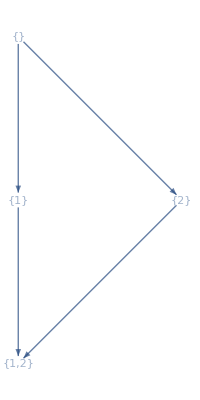

# twists | 0 | 1 | 2
# functions | 1 | 2 | 1

```mathematica
funcTree@list
```

#### Twist replacements

Replacement operation at each vertex:

```mathematica
rr[1][f_]:=replace[1,4]@f
rr[2][f_]:=replace[2,5]@f
```

Wavefunction:

```mathematica
ψ=⟨1,2⟩+⟨2,3⟩+⟨3,1⟩;
```

Generate basis functions:

```mathematica
Subscript[f, {}]==(Subscript[F, {}]=ψ)

Table[Subscript[f, nn[[2]][[j]]]==(Subscript[F, nn[[2]][[j]]]=ψ//rr[nn[[2]][[j]][[1]]]),{j,Length@nn[[2]]}]//Column

Table[Subscript[f, nn[[3]][[j]]]==(Subscript[F, nn[[3]][[j]]]=ψ//rr[nn[[3]][[j]][[1]]]//rr[nn[[3]][[j]][[2]]]),{j,Length@nn[[3]]}]//Column
```

f_{}==⟨1,2⟩+⟨2,3⟩+⟨3,1⟩

f_{1}==⟨2,3⟩-⟨2,4⟩+⟨3,4⟩
f_{2}==-⟨1,3⟩+⟨1,5⟩-⟨3,5⟩

f_{1,2}==⟨3,4⟩-⟨3,5⟩+⟨4,5⟩

### f_{_} Eplicit form

he list of all functions f graded by weight is given by

```mathematica
allf={Subscript[f, {}],Table[Subscript[f, nn[[2]][[j]]],{j,Length@nn[[2]]}],
Table[Subscript[f, nn[[3]][[j]]],{j,Length@nn[[3]]}]}
```

{f_{},{f_{1},f_{2}},{f_{1,2}}}

The expression for all f are given by

```mathematica
evalfRule=Join[{Subscript[f, {}]->ψ},Table[Rule[Subscript[f, nn[[2]][[j]]],(Subscript[F, nn[[2]][[j]]]=ψ//rr[nn[[2]][[j]][[1]]])],{j,Length@nn[[2]]}],Table[Rule[Subscript[f, nn[[3]][[j]]],(Subscript[F, nn[[3]][[j]]]=ψ//rr[nn[[3]][[j]][[1]]]//rr[nn[[3]][[j]][[2]]])],{j,Length@nn[[3]]}]]
```

{f_{}→⟨1,2⟩+⟨2,3⟩+⟨3,1⟩,f_{1}→⟨2,3⟩-⟨2,4⟩+⟨3,4⟩,f_{2}→-⟨1,3⟩+⟨1,5⟩-⟨3,5⟩,f_{1,2}→⟨3,4⟩-⟨3,5⟩+⟨4,5⟩}

Each bracket represent the canonical form of a simplex. Which in standard coordinates id given by the function simplex

```mathematica
Clear[simplex]
simplex[I__]:= Det[P/@{I,0}]/(Product[L[i],{i,{I}}] L[0])
```

For example

```mathematica
simplex[1,2]
```

1/((x1+X1+Y) (x2+X2+Y))

Therefore we can evaluate f using

```mathematica
evalf[exp_]:=exp/. evalfRule/. AngleBracket-> simplex
```

```mathematica
evalf[Subscript[f, {}]]
%//Factor
```

-1/((x1+X1+x2+X2) (x1+X1+Y))-1/((x1+X1+x2+X2) (x2+X2+Y))+1/((x1+X1+Y) (x2+X2+Y))

-(2 Y)/((x1+X1+x2+X2) (x1+X1+Y) (x2+X2+Y))

### Differential equations

```mathematica
solveCoeff;
fsub={Subscript[f, {}]->"ψ",Subscript[f, {1}]->"F",Subscript[f, {2}]->"F̃",Subscript[f, {1,2}]->"Z"};
```

```mathematica
dfeq=Flatten@Table[eqlvl[l][[m]],{l,3},{m,Length@nn[[l]]}];
dfeq/.fsub//Column
```

d[ψ]==F dL_(X1-Y)+F̃ dL_(X2-Y)+(-F+ψ) dL_(X1+Y)+(-F̃+ψ) dL_(X2+Y)
d[F]==Z dL_(X1+X2)+F dL_(X1-Y)+(F-Z) dL_(X2+Y)
d[F̃]==Z dL_(X1+X2)+F̃ dL_(X2-Y)+(F̃-Z) dL_(X1+Y)
d[Z]==2 Z dL_(X1+X2)

### A matrix

```mathematica
nsite=2;
flist=Flatten[Table[Subscript[f, nn[[l]][[m]]],{l,nsite+1},{m,Length@nn[[l]]}],1];
```

```mathematica
Flatten[Table[eqlvl[i][[m]][[2]],{i,0,nsite+1},{m,Length@eqlvl[i]}],1];
Amtx=Table[Coefficient[%[[i]],flist],{i,4^(nsite-1)}];
```

```mathematica
Amtx//MatrixForm
```

(dL_(X1+Y)+dL_(X2+Y) | dL_(X1-Y)-dL_(X1+Y) | dL_(X2-Y)-dL_(X2+Y) | 0
0 | dL_(X1-Y)+dL_(X2+Y) | 0 | dL_(X1+X2)-dL_(X2+Y)
0 | 0 | dL_(X2-Y)+dL_(X1+Y) | dL_(X1+X2)-dL_(X1+Y)
0 | 0 | 0 | 2 dL_(X1+X2))

Check flatness:

```mathematica
A=Amtx/.Subscript[dL, a_]:>Dt@Log[a];
vars={X1,X2,Y};
DeleteDuplicates@Flatten@Table[Coefficient[A,Dt[vars[[i]]]].Coefficient[A,Dt[vars[[j]]]]-Coefficient[A,Dt[vars[[j]]]].Coefficient[A,Dt[vars[[i]]]]//Simplify,{i,Length@vars},{j,Length@vars}]
```

{0}

### d^2=0

Generate 3-letter relations:

```mathematica
DeleteDuplicates@DeleteCases[Flatten[Table[If[(Subscript[dL, letters[[i]]]⋀Subscript[dL, letters[[k]]]+Subscript[dL, letters[[j]]]⋀Subscript[dL, letters[[i]]]-Subscript[dL, letters[[j]]]⋀Subscript[dL, letters[[k]]]/.Subscript[dL, x_]:>Dt@Log@x/.Dt->dL/.Dt->dL/.dL[a_]:>Subscript[dL, a]//dLsimp)===0∧i=!=j∧i=!=k∧j=!=k,{i,j,k},0],{i,Length@letters},{j,Length@letters},{k,Length@letters}],2],0];
reltab=Subscript[dL, letters[[#1]]]⋀Subscript[dL, letters[[#3]]]+Subscript[dL, letters[[#2]]]⋀Subscript[dL, letters[[#1]]]-Subscript[dL, letters[[#2]]]⋀Subscript[dL, letters[[#3]]]&@@@%//dLsimp;
```

Independent relations:

```mathematica
dLrel=Table[If[reltab[[i,1]][[1]]===-1,-reltab[[i]],reltab[[i]]],{i,Length@reltab}]//DeleteDuplicates
dLsub=Table[%[[i]][[1]]->-%[[i]][[2]]-%[[i]][[3]],{i,Length@%}];
dLsub=Table[dLrel[[i]][[1]]->Subscript[R, i]-dLrel[[i]][[2]]-dLrel[[i]][[3]],{i,Length@dLrel}];
%//Length
```

{dL_(X1+X2)⋀dL_(X1-Y)-dL_(X1+X2)⋀dL_(X2+Y)+dL_(X1-Y)⋀dL_(X2+Y),dL_(X1+X2)⋀dL_(X2-Y)-dL_(X1+X2)⋀dL_(X1+Y)+dL_(X2-Y)⋀dL_(X1+Y)}

2

Taking d^2:

```mathematica
dfsub=dfeq/.a_==b_:>a->b;
ddeq=Flatten@Table[d[Subscript[f, nn[[l]][[m]]]],{l,3},{m,Length@nn[[l]]}]/.d[f_]:>(d^2)[f]==dd[f];
```

Substituting three-letter relations:

```mathematica
ddeq/.dLsub/.fsub//Simplify//Column
```

d^2[ψ]==Z (R_1+R_2)
d^2[F]==Z R_1
d^2[F̃]==Z R_2
d^2[Z]==0

### Symbol

A matrix in the dS limit:

```mathematica
flist2=flist/.Subscript[f, a_]:>ϵ^(-Length@a)Subscript[f, a];
Series[ϵ (Amtx.flist2)/(flist2/.Subscript[f, __]->1),{ϵ,0,0}]//Normal;
Amtxeps0=Table[Coefficient[%[[i]],flist],{i,4^(nsite-1)}];
Amtxeps0//MatrixForm
```

(0 | dL_(X1-Y)-dL_(X1+Y) | dL_(X2-Y)-dL_(X2+Y) | 0
0 | 0 | 0 | dL_(X1+X2)-dL_(X2+Y)
0 | 0 | 0 | dL_(X1+X2)-dL_(X1+Y)
0 | 0 | 0 | 0)

Symbol from differential equations:

```mathematica
Sym3=S/@flist;
Amtxeps0.flist/.Subscript[dL, a_]:>dLog[a]/.dLog[a_]-dLog[b_]:>dLog[a/b]/.Subscript[f, {1,2}]:>1;
A3eq=%/.Subscript[f, a_] dLog[x_]:>S[Subscript[f, a]]⊗x/. dLog[x_]:>x;
Symrule=Table[Sym3[[i]]->%[[i]],{i,4}];
```

```mathematica
Sdiff=A3eq[[1]]//.Symrule//TensorSimp
```

(X1+X2)/(X1+Y)⊗(X2-Y)/(X2+Y)+(X1+X2)/(X2+Y)⊗(X1-Y)/(X1+Y)

## 2-site chain ϵ = 0

### Definitions

```mathematica
nsite=2;
```

Projective planes:

```mathematica
X={x1,x2,1};
P[1]={1,0,X1+Y};
P[2]={0,1,X2+Y};
P[3]={1,1,X1+X2};

P[4]={1,0,0};
P[5]={0,1,0};
P[0]={0,0,1};
L[i_]:=P[i].X
planes=Table[L[i],{i,5}]
```

{x1+X1+Y,x2+X2+Y,x1+X1+x2+X2,x1,x2}

Generate letters:

```mathematica
planes[[;;3]]/.x1->0/.x2->0;
Ysub=Subsets[{Y},2]/.Y->(Y->-Y);
letters=Table[%%/.Ysub[[i]],{i,Length@Ysub}]//Flatten//DeleteDuplicates//Sort
flip=Table[Rule[{#1[[i]]},{#2[[i]]}]&[-letters,letters],{i,Length@letters}];
logs=Log/@letters;
```

{X1+X2,X1-Y,X2-Y,X1+Y,X2+Y}

## 3-site chain

### Definitions

```mathematica
nsite=3;
```

Projective planes:

```mathematica
X={x1,x2,x3,1};
P[1]={1,0,0,X1+Y12};
P[2]={0,1,0,X2+Y12+Y23};
P[3]={0,0,1,X3+Y23};
P[4]={1,1,1,X1+X2+X3};
P[5]={1,1,0,X1+X2+Y23};
P[6]={0,1,1,X2+X3+Y12};

P[7]={1,0,0,0};
P[8]={0,1,0,0};
P[9]={0,0,1,0};
P[10]={0,0,0,1};
L[i_]:=P[i].X
planes=Table[L[i],{i,9}]
```

{x1+X1+Y12,x2+X2+Y12+Y23,x3+X3+Y23,x1+X1+x2+X2+x3+X3,x1+X1+x2+X2+Y23,x2+X2+x3+X3+Y12,x1,x2,x3}

Generate letters:

```mathematica
planes[[;;6]]/.x1->0/.x2->0/.x3->0;
Ysub=Subsets[{Y12,Y23},2]/.Y12->(Y12->-Y12)/.Y23->(Y23->-Y23);
letters=Table[%%/.Ysub[[i]],{i,Length@Ysub}]//Flatten//DeleteDuplicates//Sort
flip=Table[Rule[{#1[[i]]},{#2[[i]]}]&[-letters,letters],{i,Length@letters}];
```

{X1+X2+X3,X1-Y12,X2+X3-Y12,X1+Y12,X2+X3+Y12,X1+X2-Y23,X3-Y23,X2-Y12-Y23,X2+Y12-Y23,X1+X2+Y23,X3+Y23,X2-Y12+Y23,X2+Y12+Y23}

### Basis functions

#### Function tree

Function labels:

```mathematica
Table[{1,Subscript[2, i],3},{i,3}];
list=Flatten[Table[Subsets[%[[i]],3],{i,Length@%}],1]//DeleteDuplicates
nn=Cases[list//Sort,#]&/@Table[_,{i,0,3},{j,i}];
```

{{},{1},{2_1},{3},{1,2_1},{1,3},{2_1,3},{1,2_1,3},{2_2},{1,2_2},{2_2,3},{1,2_2,3},{2_3},{1,2_3},{2_3,3},{1,2_3,3}}

Tree structure and the number of functions in each twist layer:

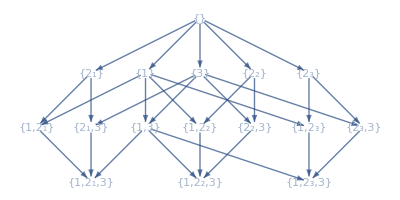

# twists | 0 | 1 | 2 | 3
# functions | 1 | 5 | 7 | 3

```mathematica
funcTree@list
```

Here is the interpretation with tubing. You can see the notation i_j appearing on the first arrows of the graph.

-Graphics-

The first step of the tree correspond to the  growth of the tubing so I guess i_j means activate site i and grow in towards j . The symbol 2_2 correspond to growth towards both directions

-Graphics-

#### Twist replacements

Replacement operations at each vertex:

```mathematica
rr[1][f_]:=replace[1,7]@f
rr[Subscript[2, 2]][f_]:=replace[{2,5,6},8]@f
rr[Subscript[2, 1]][f_]:=replace[{2,6},8]@f-replace[{2,5,6},8]@f
rr[Subscript[2, 3]][f_]:=replace[{2,5},8]@f-replace[{2,5,6},8]@f
rr[3][f_]:=replace[3,9]@f
```

Wavefunction:

```mathematica
ψ=⟨1,2,3⟩-⟨1,2,6⟩-⟨1,3,4⟩+⟨1,3,5⟩+⟨1,3,6⟩-⟨1,4,5⟩-⟨2,3,5⟩+⟨2,4,5⟩-⟨2,4,6⟩+⟨3,4,6⟩;
```

Generate basis functions:

```mathematica
Subscript[f, {}]==(Subscript[F, {}]=ψ);

Table[Subscript[f, nn[[2]][[j]]]==(Subscript[F, nn[[2]][[j]]]=ψ//rr[nn[[2]][[j]][[1]]]),{j,Length@nn[[2]]}]//Column

Table[Subscript[f, nn[[3]][[j]]]==(Subscript[F, nn[[3]][[j]]]=ψ//rr[nn[[3]][[j]][[1]]]//rr[nn[[3]][[j]][[2]]]),{j,Length@nn[[3]]}]//Column;

Table[Subscript[f, nn[[4]][[j]]]==(Subscript[F, nn[[4]][[j]]]=ψ//rr[nn[[4]][[j]][[1]]]//rr[nn[[4]][[j]][[2]]]//rr[nn[[4]][[j]][[3]]]),{j,Length@nn[[4]]}]//Column;
```

f_{1}==-⟨2,3,5⟩+⟨2,3,7⟩+⟨2,4,5⟩-⟨2,4,6⟩-⟨2,6,7⟩+⟨3,4,6⟩-⟨3,4,7⟩+⟨3,5,7⟩+⟨3,6,7⟩-⟨4,5,7⟩
f_{3}==-⟨1,2,6⟩+⟨1,2,9⟩-⟨1,4,5⟩+⟨1,4,9⟩-⟨1,5,9⟩-⟨1,6,9⟩+⟨2,4,5⟩-⟨2,4,6⟩+⟨2,5,9⟩+⟨4,6,9⟩
f_{2_1}==⟨1,3,5⟩-⟨1,3,8⟩-⟨1,4,5⟩+⟨1,4,8⟩-⟨3,5,8⟩+⟨4,5,8⟩
f_{2_2}==-⟨1,3,4⟩+⟨1,3,8⟩-⟨1,4,8⟩+⟨3,4,8⟩
f_{2_3}==⟨1,3,6⟩-⟨1,3,8⟩+⟨1,6,8⟩+⟨3,4,6⟩-⟨3,4,8⟩-⟨4,6,8⟩

### f_{_} Eplicit form

he list of all functions f graded by weight is given by

```mathematica
allf={Subscript[f, {}],Table[Subscript[f, nn[[2]][[j]]],{j,Length@nn[[2]]}],
Table[Subscript[f, nn[[3]][[j]]],{j,Length@nn[[3]]}],Table[Subscript[f, nn[[4]][[j]]],{j,Length@nn[[4]]}]}
```

{f_{},{f_{1},f_{3},f_{2_1},f_{2_2},f_{2_3}},{f_{1,3},f_{1,2_1},f_{1,2_2},f_{1,2_3},f_{2_1,3},f_{2_2,3},f_{2_3,3}},{f_{1,2_1,3},f_{1,2_2,3},f_{1,2_3,3}}}

The expression for all f are given by

```mathematica
(evalfRule=Join[{Subscript[f, {}]->ψ},Table[Rule[Subscript[f, nn[[2]][[j]]],(Subscript[F, nn[[2]][[j]]]=ψ//rr[nn[[2]][[j]][[1]]])],{j,Length@nn[[2]]}],Table[Rule[Subscript[f, nn[[3]][[j]]],(Subscript[F, nn[[3]][[j]]]=ψ//rr[nn[[3]][[j]][[1]]]//rr[nn[[3]][[j]][[2]]])],{j,Length@nn[[3]]}],Table[Rule[Subscript[f, nn[[4]][[j]]],(Subscript[F, nn[[4]][[j]]]=ψ//rr[nn[[4]][[j]][[1]]]//rr[nn[[4]][[j]][[2]]]//rr[nn[[4]][[j]][[3]]])],{j,Length@nn[[4]]}]])//Short
```

{f_{}→⟨1,2,3⟩-⟨1,2,6⟩-⟨1,3,4⟩+⟨1,3,5⟩+⟨1,3,6⟩-⟨1,4,5⟩-⟨2,3,5⟩+⟨2,4,5⟩-⟨2,4,6⟩+⟨3,4,6⟩,«14»,f_{1,2_3,3}→-⟨4,6,8⟩+⟨4,6,9⟩-⟨4,8,9⟩-⟨6,7,8⟩+⟨6,7,9⟩+⟨7,8,9⟩}

Each bracket represent the canonical form of a simplex. Which in standard coordinates id given by the function simplex.  To write an explicit expression we introduce and arbitrary hyperplane

```mathematica
P[0]={a,b,c,d};
```

```mathematica
Clear[simplex]
simplex[I__]:= Det[P/@{I,0}]/(Product[L[i],{i,{I}} ]L[0])
```

For example

```mathematica
simplex[1,2,3]
```

(d-a X1-b X2-c X3-a Y12-b Y12-b Y23-c Y23)/((d+a x1+b x2+c x3) (x1+X1+Y12) (x3+X3+Y23) (x2+X2+Y12+Y23))

Therefore we can evaluate f using

```mathematica
evalf[exp_]:=exp/. evalfRule/. AngleBracket-> simplex
```

```mathematica
evalf[Subscript[f, {}]]//Factor
```

(4 Y12 Y23 (x1+X1+2 x2+2 X2+x3+X3+Y12+Y23))/((x1+X1+x2+X2+x3+X3) (x1+X1+Y12) (x2+X2+x3+X3+Y12) (x1+X1+x2+X2+Y23) (x3+X3+Y23) (x2+X2+Y12+Y23))

Notice that the forms are independent of P[0]

```mathematica
evalf[Subscript[f, {1,Subscript[2, 2],3}]]
```

-d/(x1 x2 x3 (d+a x1+b x2+c x3))+(d-a X1-a X2-a X3)/(x2 x3 (d+a x1+b x2+c x3) (x1+X1+x2+X2+x3+X3))-(-d+b X1+b X2+b X3)/(x1 x3 (d+a x1+b x2+c x3) (x1+X1+x2+X2+x3+X3))+(d-c X1-c X2-c X3)/(x1 x2 (d+a x1+b x2+c x3) (x1+X1+x2+X2+x3+X3))

```mathematica
evalf[allf]//Factor
```

{(4 Y12 Y23 (x1+X1+2 x2+2 X2+x3+X3+Y12+Y23))/((x1+X1+x2+X2+x3+X3) (x1+X1+Y12) (x2+X2+x3+X3+Y12) (x1+X1+x2+X2+Y23) (x3+X3+Y23) (x2+X2+Y12+Y23)),{(2 (-X1+Y12) Y23 (x1+X1+2 x2+2 X2+x3+X3+Y12+Y23))/(x1 (x1+X1+x2+X2+x3+X3) (x2+X2+x3+X3+Y12) (x1+X1+x2+X2+Y23) (x3+X3+Y23) (x2+X2+Y12+Y23)),-(2 Y12 (X3-Y23) (x1+X1+2 x2+2 X2+x3+X3+Y12+Y23))/(x3 (x1+X1+x2+X2+x3+X3) (x1+X1+Y12) (x2+X2+x3+X3+Y12) (x1+X1+x2+X2+Y23) (x2+X2+Y12+Y23)),((x1+X1+x2+X2-Y23) (X2-Y12+Y23))/(x2 (x1+X1+x2+X2+x3+X3) (x1+X1+Y12) (x1+X1+x2+X2+Y23) (x3+X3+Y23)),-(X2-Y12-Y23)/(x2 (x1+X1+x2+X2+x3+X3) (x1+X1+Y12) (x3+X3+Y23)),((x2+X2+x3+X3-Y12) (X2+Y12-Y23))/(x2 (x1+X1+x2+X2+x3+X3) (x1+X1+Y12) (x2+X2+x3+X3+Y12) (x3+X3+Y23))},{((X1-Y12) (X3-Y23) (x1+X1+2 x2+2 X2+x3+X3+Y12+Y23))/(x1 x3 (x1+X1+x2+X2+x3+X3) (x2+X2+x3+X3+Y12) (x1+X1+x2+X2+Y23) (x2+X2+Y12+Y23)),((x1+X1+x2+X2-Y23) (X1+X2+Y23))/(x1 x2 (x1+X1+x2+X2+x3+X3) (x1+X1+x2+X2+Y23) (x3+X3+Y23)),-(X1+X2-Y23)/(x1 x2 (x1+X1+x2+X2+x3+X3) (x3+X3+Y23)),((X1+x2+X2+x3+X3) (X2+Y12-Y23))/(x1 x2 (x1+X1+x2+X2+x3+X3) (x2+X2+x3+X3+Y12) (x3+X3+Y23)),-((x1+X1+x2+X2+X3) (-X2+Y12-Y23))/(x2 x3 (x1+X1+x2+X2+x3+X3) (x1+X1+Y12) (x1+X1+x2+X2+Y23)),-(X2+X3-Y12)/(x2 x3 (x1+X1+x2+X2+x3+X3) (x1+X1+Y12)),((x2+X2+x3+X3-Y12) (X2+X3+Y12))/(x2 x3 (x1+X1+x2+X2+x3+X3) (x1+X1+Y12) (x2+X2+x3+X3+Y12))},{((x1+X1+x2+X2+X3) (X1+X2+Y23))/(x1 x2 x3 (x1+X1+x2+X2+x3+X3) (x1+X1+x2+X2+Y23)),-(X1+X2+X3)/(x1 x2 x3 (x1+X1+x2+X2+x3+X3)),((X1+x2+X2+x3+X3) (X2+X3+Y12))/(x1 x2 x3 (x1+X1+x2+X2+x3+X3) (x2+X2+x3+X3+Y12))}}

### Differential equations

```mathematica
solveCoeff;
fsub={Subscript[f, {}]->"ψ",
Subscript[f, {1}]->"F",Subscript[f, {Subscript[2, 1]}]->"Q_1",Subscript[f, {Subscript[2, 2]}]->"Q_2",Subscript[f, {Subscript[2, 3]}]->"Q_3",Subscript[f, {3}]->"F̃",
Subscript[f, {1,Subscript[2, 1]}]->"q_1",Subscript[f, {1,Subscript[2, 2]}]->"q_2",Subscript[f, {1,Subscript[2, 3]}]->"q_3",Subscript[f, {1,3}]->"f",Subscript[f, {Subscript[2, 1],3}]->"(q̃)_3",Subscript[f, {Subscript[2, 2],3}]->"(q̃)_2",Subscript[f, {Subscript[2, 3],3}]->"(q̃)_1",
Subscript[f, {1,Subscript[2, 1],3}]->"g",Subscript[f, {1,Subscript[2, 2],3}]->"Z",Subscript[f, {1,Subscript[2, 3],3}]->"g̃"};
```

```mathematica
dfeq=Flatten@Table[eqlvl[l][[m]],{l,4},{m,Length@nn[[l]]}];
dfeq/.fsub//Column
```

d[ψ]==F dL_(X1-Y12)+(-F+ψ) dL_(X1+Y12)+F̃ dL_(X3-Y23)+Q_2 dL_(X2-Y12-Y23)+Q_3 dL_(X2+Y12-Y23)+(-F̃+ψ) dL_(X3+Y23)+Q_1 dL_(X2-Y12+Y23)+(-Q_1-Q_2-Q_3+ψ) dL_(X2+Y12+Y23)
d[F]==F dL_(X1-Y12)+q_2 dL_(X1+X2-Y23)+f dL_(X3-Y23)+q_3 dL_(X2+Y12-Y23)+q_1 dL_(X1+X2+Y23)+(-f+F) dL_(X3+Y23)+(F-q_1-q_2-q_3) dL_(X2+Y12+Y23)
d[F̃]==f dL_(X1-Y12)+(q̃)_2 dL_(X2+X3-Y12)+(-f+F̃) dL_(X1+Y12)+(q̃)_1 dL_(X2+X3+Y12)+F̃ dL_(X3-Y23)+(q̃)_3 dL_(X2-Y12+Y23)+(F̃-(q̃)_1-(q̃)_2-(q̃)_3) dL_(X2+Y12+Y23)
d[Q_1]==-(q̃)_2 dL_(X2+X3-Y12)+(-q_1+Q_1) dL_(X1+Y12)+((q̃)_2+(q̃)_3) dL_(X3-Y23)+q_1 dL_(X1+X2+Y23)+(-(q̃)_3+Q_1) dL_(X3+Y23)+Q_1 dL_(X2-Y12+Y23)
d[Q_2]==(q̃)_2 dL_(X2+X3-Y12)+(-q_2+Q_2) dL_(X1+Y12)+q_2 dL_(X1+X2-Y23)+Q_2 dL_(X2-Y12-Y23)+(-(q̃)_2+Q_2) dL_(X3+Y23)
d[Q_3]==(q_2+q_3) dL_(X1-Y12)+(-q_3+Q_3) dL_(X1+Y12)+(q̃)_1 dL_(X2+X3+Y12)-q_2 dL_(X1+X2-Y23)+Q_3 dL_(X2+Y12-Y23)+(-(q̃)_1+Q_3) dL_(X3+Y23)
d[f]==Z dL_(X1+X2+X3)+f dL_(X1-Y12)+g̃ dL_(X2+X3+Y12)+f dL_(X3-Y23)+g dL_(X1+X2+Y23)+(f-g-g̃-Z) dL_(X2+Y12+Y23)
d[q_1]==-Z dL_(X1+X2+X3)+(g+Z) dL_(X3-Y23)+2 q_1 dL_(X1+X2+Y23)+(-g+q_1) dL_(X3+Y23)
d[q_2]==Z dL_(X1+X2+X3)+2 q_2 dL_(X1+X2-Y23)+(q_2-Z) dL_(X3+Y23)
d[q_3]==(q_2+q_3) dL_(X1-Y12)+g̃ dL_(X2+X3+Y12)-q_2 dL_(X1+X2-Y23)+q_3 dL_(X2+Y12-Y23)+(-g̃+q_3) dL_(X3+Y23)
d[(q̃)_3]==-(q̃)_2 dL_(X2+X3-Y12)+(-g+(q̃)_3) dL_(X1+Y12)+((q̃)_2+(q̃)_3) dL_(X3-Y23)+g dL_(X1+X2+Y23)+(q̃)_3 dL_(X2-Y12+Y23)
d[(q̃)_2]==Z dL_(X1+X2+X3)+2 (q̃)_2 dL_(X2+X3-Y12)+((q̃)_2-Z) dL_(X1+Y12)
d[(q̃)_1]==-Z dL_(X1+X2+X3)+(g̃+Z) dL_(X1-Y12)+(-g̃+(q̃)_1) dL_(X1+Y12)+2 (q̃)_1 dL_(X2+X3+Y12)
d[g]==-Z dL_(X1+X2+X3)+(g+Z) dL_(X3-Y23)+2 g dL_(X1+X2+Y23)
d[Z]==3 Z dL_(X1+X2+X3)
d[g̃]==-Z dL_(X1+X2+X3)+(g̃+Z) dL_(X1-Y12)+2 g̃ dL_(X2+X3+Y12)

### A matrix

```mathematica
flist=Flatten[Table[Subscript[f, nn[[l]][[m]]],{l,nsite+1},{m,Length@nn[[l]]}],1];
```

```mathematica
Flatten[Table[eqlvl[i][[m]][[2]],{i,0,nsite+1},{m,Length@eqlvl[i]}],1];
Amtx=Table[Coefficient[%[[i]],flist],{i,4^(nsite-1)}];
```

```mathematica
Amtx//MatrixForm
```

(dL_(X1+Y12)+dL_(X3+Y23)+dL_(X2+Y12+Y23) | dL_(X1-Y12)-dL_(X1+Y12) | dL_(X3-Y23)-dL_(X3+Y23) | dL_(X2-Y12+Y23)-dL_(X2+Y12+Y23) | dL_(X2-Y12-Y23)-dL_(X2+Y12+Y23) | dL_(X2+Y12-Y23)-dL_(X2+Y12+Y23) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | dL_(X1-Y12)+dL_(X3+Y23)+dL_(X2+Y12+Y23) | 0 | 0 | 0 | 0 | dL_(X3-Y23)-dL_(X3+Y23) | dL_(X1+X2+Y23)-dL_(X2+Y12+Y23) | dL_(X1+X2-Y23)-dL_(X2+Y12+Y23) | dL_(X2+Y12-Y23)-dL_(X2+Y12+Y23) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | dL_(X1+Y12)+dL_(X3-Y23)+dL_(X2+Y12+Y23) | 0 | 0 | 0 | dL_(X1-Y12)-dL_(X1+Y12) | 0 | 0 | 0 | dL_(X2-Y12+Y23)-dL_(X2+Y12+Y23) | dL_(X2+X3-Y12)-dL_(X2+Y12+Y23) | dL_(X2+X3+Y12)-dL_(X2+Y12+Y23) | 0 | 0 | 0
0 | 0 | 0 | dL_(X1+Y12)+dL_(X3+Y23)+dL_(X2-Y12+Y23) | 0 | 0 | 0 | -dL_(X1+Y12)+dL_(X1+X2+Y23) | 0 | 0 | dL_(X3-Y23)-dL_(X3+Y23) | -dL_(X2+X3-Y12)+dL_(X3-Y23) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | dL_(X1+Y12)+dL_(X2-Y12-Y23)+dL_(X3+Y23) | 0 | 0 | 0 | -dL_(X1+Y12)+dL_(X1+X2-Y23) | 0 | 0 | dL_(X2+X3-Y12)-dL_(X3+Y23) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | dL_(X1+Y12)+dL_(X2+Y12-Y23)+dL_(X3+Y23) | 0 | 0 | dL_(X1-Y12)-dL_(X1+X2-Y23) | dL_(X1-Y12)-dL_(X1+Y12) | 0 | 0 | dL_(X2+X3+Y12)-dL_(X3+Y23) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | dL_(X1-Y12)+dL_(X3-Y23)+dL_(X2+Y12+Y23) | 0 | 0 | 0 | 0 | 0 | 0 | dL_(X1+X2+Y23)-dL_(X2+Y12+Y23) | dL_(X1+X2+X3)-dL_(X2+Y12+Y23) | dL_(X2+X3+Y12)-dL_(X2+Y12+Y23)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 dL_(X1+X2+Y23)+dL_(X3+Y23) | 0 | 0 | 0 | 0 | 0 | dL_(X3-Y23)-dL_(X3+Y23) | -dL_(X1+X2+X3)+dL_(X3-Y23) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 dL_(X1+X2-Y23)+dL_(X3+Y23) | 0 | 0 | 0 | 0 | 0 | dL_(X1+X2+X3)-dL_(X3+Y23) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | dL_(X1-Y12)-dL_(X1+X2-Y23) | dL_(X1-Y12)+dL_(X2+Y12-Y23)+dL_(X3+Y23) | 0 | 0 | 0 | 0 | 0 | dL_(X2+X3+Y12)-dL_(X3+Y23)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | dL_(X1+Y12)+dL_(X3-Y23)+dL_(X2-Y12+Y23) | -dL_(X2+X3-Y12)+dL_(X3-Y23) | 0 | -dL_(X1+Y12)+dL_(X1+X2+Y23) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 dL_(X2+X3-Y12)+dL_(X1+Y12) | 0 | 0 | dL_(X1+X2+X3)-dL_(X1+Y12) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | dL_(X1+Y12)+2 dL_(X2+X3+Y12) | 0 | -dL_(X1+X2+X3)+dL_(X1-Y12) | dL_(X1-Y12)-dL_(X1+Y12)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | dL_(X3-Y23)+2 dL_(X1+X2+Y23) | -dL_(X1+X2+X3)+dL_(X3-Y23) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 dL_(X1+X2+X3) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -dL_(X1+X2+X3)+dL_(X1-Y12) | dL_(X1-Y12)+2 dL_(X2+X3+Y12))

Check flatness:

```mathematica
A=Amtx/.Subscript[dL, a_]:>Dt@Log[a];
vars={X1,X2,X3,Y12,Y23};
DeleteDuplicates@Flatten@Table[Coefficient[A,Dt[vars[[i]]]].Coefficient[A,Dt[vars[[j]]]]-Coefficient[A,Dt[vars[[j]]]].Coefficient[A,Dt[vars[[i]]]]//Simplify,{i,Length@vars},{j,Length@vars}]
```

{0}

### d^2=0

List of letters:

```mathematica
Bsub={X1+Y12->B[1],X2+Y12+Y23->B[2],X3+Y23->B[3],X1+X2+X3->B[4],X1+X2+Y23->B[5],X2+X3+Y12->B[6],
X1-Y12->B[7],X2-Y12+Y23->B[8],X2+Y12-Y23->B[9],X2-Y12-Y23->B[10],X3-Y23->B[11],X1+X2-Y23->B[12],X2+X3-Y12->B[13]};
Blist=Bsub[[;;,1]]
```

{X1+Y12,X2+Y12+Y23,X3+Y23,X1+X2+X3,X1+X2+Y23,X2+X3+Y12,X1-Y12,X2-Y12+Y23,X2+Y12-Y23,X2-Y12-Y23,X3-Y23,X1+X2-Y23,X2+X3-Y12}

Three-letter relations:

```mathematica
Rlist={{4,5,11},{3,4,12},{4,6,7},{1,4,13},{2,5,7},{1,5,8},{7,9,12},{1,10,12},{2,6,11},{3,6,9},{8,11,13},{3,10,13}};
dLsub=Table[Subscript[dL, Blist[[Rlist[[i,1]]]]]⋀Subscript[dL, Blist[[Rlist[[i,2]]]]]->Subscript[R, i]-Subscript[dL, Blist[[Rlist[[i,2]]]]]⋀Subscript[dL, Blist[[Rlist[[i,3]]]]]-Subscript[dL, Blist[[Rlist[[i,3]]]]]⋀Subscript[dL, Blist[[Rlist[[i,1]]]]]/.Bsub//dLsimp,{i,Length@Rlist}];
```

Taking d^2:

```mathematica
dfsub=dfeq/.a_==b_:>a->b/.Bsub;
ddeq=Flatten@Table[d[Subscript[f, nn[[l]][[m]]]],{l,4},{m,Length@nn[[l]]}]/.d[f_]:>(d^2)[f]==dd[f];
```

Substituting the three-letter relations:

```mathematica
ddeq/.fsub/.dLsub//Column
```

d^2[ψ]==q_1 (R_5+R_6)+q_2 (R_7-R_8)+(q̃)_1 (R_9+R_10)+(q̃)_2 (-R_11-R_12)
d^2[F]==Z (-R_1+R_2)+q_1 R_5+q_2 R_7+g̃ (R_9+R_10)
d^2[F̃]==Z (-R_3+R_4)+g (R_5+R_6)+(q̃)_1 R_9-(q̃)_2 R_11
d^2[Q_1]==Z (-R_1-R_4)+q_1 R_6-(q̃)_2 R_11
d^2[Q_2]==Z (R_2+R_4)-q_2 R_8-(q̃)_2 R_12
d^2[Q_3]==Z (-R_2-R_3)+q_2 R_7+(q̃)_1 R_10
d^2[f]==Z (-R_1-R_3)+g R_5+g̃ R_9
d^2[q_1]==-2 Z R_1
d^2[q_2]==2 Z R_2
d^2[q_3]==Z (-R_2-R_3)+q_2 R_7+g̃ R_10
d^2[(q̃)_3]==Z (-R_1-R_4)+g R_6-(q̃)_2 R_11
d^2[(q̃)_2]==2 Z R_4
d^2[(q̃)_1]==-2 Z R_3
d^2[g]==-2 Z R_1
d^2[Z]==0
d^2[g̃]==-2 Z R_3

### Symbol

A matrix in the dS limit:

```mathematica
flist2=flist/.Subscript[f, a_]:>ϵ^(-Length@a)Subscript[f, a];
Series[ϵ (Amtx.flist2)/(flist2/.Subscript[f, __]->1),{ϵ,0,0}]//Normal;
Amtxeps0=Table[Coefficient[%[[i]],flist],{i,4^(nsite-1)}];
```

Symbol from differential equations:

```mathematica
Φsub=Table[letters[[i]]->Φ[i],{i,Length@letters}];
Sym3=S/@flist;
```

```mathematica
Amtxeps0.flist/.Φsub/.Subscript[dL, a_]:>dLog[a]/.dLog[a_]-dLog[b_]:>dLog[a/b]/.Subscript[f, {1,Subscript[2, n_],3}]:>(-1)^n;
A3eq=%/.Subscript[f, a_] dLog[x_]:>S[Subscript[f, a]]⊗x/. dLog[x_]:>x;
Symrule=Table[Sym3[[i]]->%[[i]],{i,16}];
```

```mathematica
Sdiff=A3eq[[1]]//.Symrule//TensorSimp
Length@%
```

Φ[1]⊗Φ[2]⊗Φ[7]+Φ[1]⊗Φ[2]⊗Φ[9]-Φ[1]⊗Φ[2]⊗Φ[11]-Φ[1]⊗Φ[2]⊗Φ[13]+Φ[1]⊗Φ[3]⊗Φ[7]+Φ[1]⊗Φ[3]⊗Φ[8]-Φ[1]⊗Φ[3]⊗Φ[11]-Φ[1]⊗Φ[3]⊗Φ[12]-Φ[1]⊗Φ[4]⊗Φ[7]-Φ[1]⊗Φ[4]⊗Φ[8]+Φ[1]⊗Φ[4]⊗Φ[11]+Φ[1]⊗Φ[4]⊗Φ[12]-Φ[1]⊗Φ[5]⊗Φ[7]-Φ[1]⊗Φ[5]⊗Φ[9]+Φ[1]⊗Φ[5]⊗Φ[11]+Φ[1]⊗Φ[5]⊗Φ[13]+Φ[1]⊗Φ[6]⊗Φ[2]-Φ[1]⊗Φ[6]⊗Φ[4]+Φ[1]⊗Φ[6]⊗Φ[8]-Φ[1]⊗Φ[6]⊗Φ[9]+Φ[1]⊗Φ[7]⊗Φ[2]-Φ[1]⊗Φ[7]⊗Φ[4]+Φ[1]⊗Φ[7]⊗Φ[12]-Φ[1]⊗Φ[7]⊗Φ[13]-Φ[1]⊗Φ[10]⊗Φ[2]+Φ[1]⊗Φ[10]⊗Φ[4]-Φ[1]⊗Φ[10]⊗Φ[12]+Φ[1]⊗Φ[10]⊗Φ[13]-Φ[1]⊗Φ[11]⊗Φ[2]+Φ[1]⊗Φ[11]⊗Φ[4]-Φ[1]⊗Φ[11]⊗Φ[8]+Φ[1]⊗Φ[11]⊗Φ[9]-Φ[4]⊗Φ[3]⊗Φ[7]-Φ[4]⊗Φ[3]⊗Φ[8]+Φ[4]⊗Φ[3]⊗Φ[11]+Φ[4]⊗Φ[3]⊗Φ[12]+Φ[4]⊗Φ[5]⊗Φ[7]+Φ[4]⊗Φ[5]⊗Φ[9]-Φ[4]⊗Φ[5]⊗Φ[11]-Φ[4]⊗Φ[5]⊗Φ[13]+Φ[4]⊗Φ[11]⊗Φ[8]-Φ[4]⊗Φ[11]⊗Φ[9]-Φ[4]⊗Φ[11]⊗Φ[12]+Φ[4]⊗Φ[11]⊗Φ[13]+Φ[4]⊗Φ[12]⊗Φ[7]-Φ[4]⊗Φ[12]⊗Φ[11]-Φ[4]⊗Φ[13]⊗Φ[7]+Φ[4]⊗Φ[13]⊗Φ[11]-Φ[5]⊗Φ[2]⊗Φ[7]-Φ[5]⊗Φ[2]⊗Φ[9]+Φ[5]⊗Φ[2]⊗Φ[11]+Φ[5]⊗Φ[2]⊗Φ[13]+Φ[5]⊗Φ[4]⊗Φ[7]+Φ[5]⊗Φ[4]⊗Φ[9]-Φ[5]⊗Φ[4]⊗Φ[11]-Φ[5]⊗Φ[4]⊗Φ[13]-Φ[5]⊗Φ[7]⊗Φ[2]+Φ[5]⊗Φ[7]⊗Φ[4]-Φ[5]⊗Φ[9]⊗Φ[2]+Φ[5]⊗Φ[9]⊗Φ[4]+Φ[5]⊗Φ[11]⊗Φ[2]-Φ[5]⊗Φ[11]⊗Φ[4]+Φ[5]⊗Φ[13]⊗Φ[2]-Φ[5]⊗Φ[13]⊗Φ[4]-Φ[10]⊗Φ[2]⊗Φ[7]+Φ[10]⊗Φ[2]⊗Φ[11]+Φ[10]⊗Φ[4]⊗Φ[7]-Φ[10]⊗Φ[4]⊗Φ[11]-Φ[10]⊗Φ[7]⊗Φ[2]+Φ[10]⊗Φ[7]⊗Φ[4]-Φ[10]⊗Φ[7]⊗Φ[12]+Φ[10]⊗Φ[7]⊗Φ[13]+Φ[10]⊗Φ[11]⊗Φ[2]-Φ[10]⊗Φ[11]⊗Φ[4]+Φ[10]⊗Φ[11]⊗Φ[12]-Φ[10]⊗Φ[11]⊗Φ[13]-Φ[10]⊗Φ[12]⊗Φ[7]+Φ[10]⊗Φ[12]⊗Φ[11]+Φ[10]⊗Φ[13]⊗Φ[7]-Φ[10]⊗Φ[13]⊗Φ[11]+Φ[11]⊗Φ[4]⊗Φ[8]-Φ[11]⊗Φ[4]⊗Φ[9]-Φ[11]⊗Φ[4]⊗Φ[12]+Φ[11]⊗Φ[4]⊗Φ[13]-Φ[11]⊗Φ[6]⊗Φ[2]+Φ[11]⊗Φ[6]⊗Φ[4]-Φ[11]⊗Φ[6]⊗Φ[8]+Φ[11]⊗Φ[6]⊗Φ[9]+Φ[11]⊗Φ[9]⊗Φ[2]-Φ[11]⊗Φ[9]⊗Φ[4]+Φ[11]⊗Φ[10]⊗Φ[2]-Φ[11]⊗Φ[10]⊗Φ[4]+Φ[11]⊗Φ[10]⊗Φ[12]-Φ[11]⊗Φ[10]⊗Φ[13]-Φ[11]⊗Φ[13]⊗Φ[2]+Φ[11]⊗Φ[13]⊗Φ[4]+Φ[13]⊗Φ[2]⊗Φ[7]-Φ[13]⊗Φ[2]⊗Φ[11]-Φ[13]⊗Φ[4]⊗Φ[7]+Φ[13]⊗Φ[4]⊗Φ[11]+Φ[13]⊗Φ[7]⊗Φ[2]-Φ[13]⊗Φ[7]⊗Φ[4]-Φ[13]⊗Φ[11]⊗Φ[2]+Φ[13]⊗Φ[11]⊗Φ[4]

104

Symbol from discontinuity:

```mathematica
sym[1]=((X1+Y1)/(X1+X2+X3))⊗((X3+Y2)/(X3+X2-Y1)⊗(X2-Y1-Y2)/(X2-Y1+Y2)+(X2-Y1+Y2)/(X3+X2-Y1)⊗(X3-Y2)/(X3+Y2)-(X3+Y2)/(X3+X2+Y1)⊗(X2+Y1-Y2)/(X2+Y1+Y2)-(X2+Y1+Y2)/(X3+X2+Y1)⊗(X3-Y2)/(X3+Y2))/.Y1->Y12/.Y2->Y23;
sym[2]=sym[1]/.{X1->X3,X3->X1,Y12->Y23,Y23->Y12};
sym[3]=-(X1+X2+Y2)/(X1+X2+X3)⊗((X1-Y1)/(X1+Y1)⊗(X3-Y2)/(X3+Y2)+(X3-Y2)/(X3+Y2)⊗(X1-Y1)/(X1+Y1)+(X2+Y2-Y1)/(X2+Y2+Y1)⊗(X3-Y2)/(X3+Y2)+(X3-Y2)/(X3+Y2)⊗(X2+Y2-Y1)/(X2+Y2+Y1))/.Y1->Y12/.Y2->Y23;
sym[4]=sym[3]/.{X1->X3,X3->X1,Y12->Y23,Y23->Y12};
sym[5]=(X2+Y1+Y2)/(X1+X2+X3)⊗((X1-Y1)/(X1+Y1)⊗(X3-Y2)/(X3+Y2)+(X3-Y2)/(X3+Y2)⊗(X1-Y1)/(X1+Y1))/.Y1->Y12/.Y2->Y23;
```

```mathematica
Sdisc=Sum[sym[i],{i,5}]/.Φsub//TensorSimp
%//Length
```

Φ[1]⊗Φ[2]⊗Φ[7]+Φ[1]⊗Φ[2]⊗Φ[9]-Φ[1]⊗Φ[2]⊗Φ[11]-Φ[1]⊗Φ[2]⊗Φ[13]+Φ[1]⊗Φ[3]⊗Φ[7]+Φ[1]⊗Φ[3]⊗Φ[8]-Φ[1]⊗Φ[3]⊗Φ[11]-Φ[1]⊗Φ[3]⊗Φ[12]-Φ[1]⊗Φ[4]⊗Φ[7]-Φ[1]⊗Φ[4]⊗Φ[8]+Φ[1]⊗Φ[4]⊗Φ[11]+Φ[1]⊗Φ[4]⊗Φ[12]-Φ[1]⊗Φ[5]⊗Φ[7]-Φ[1]⊗Φ[5]⊗Φ[9]+Φ[1]⊗Φ[5]⊗Φ[11]+Φ[1]⊗Φ[5]⊗Φ[13]+Φ[1]⊗Φ[6]⊗Φ[2]-Φ[1]⊗Φ[6]⊗Φ[4]+Φ[1]⊗Φ[6]⊗Φ[8]-Φ[1]⊗Φ[6]⊗Φ[9]+Φ[1]⊗Φ[7]⊗Φ[2]-Φ[1]⊗Φ[7]⊗Φ[4]+Φ[1]⊗Φ[7]⊗Φ[12]-Φ[1]⊗Φ[7]⊗Φ[13]-Φ[1]⊗Φ[10]⊗Φ[2]+Φ[1]⊗Φ[10]⊗Φ[4]-Φ[1]⊗Φ[10]⊗Φ[12]+Φ[1]⊗Φ[10]⊗Φ[13]-Φ[1]⊗Φ[11]⊗Φ[2]+Φ[1]⊗Φ[11]⊗Φ[4]-Φ[1]⊗Φ[11]⊗Φ[8]+Φ[1]⊗Φ[11]⊗Φ[9]-Φ[4]⊗Φ[3]⊗Φ[7]-Φ[4]⊗Φ[3]⊗Φ[8]+Φ[4]⊗Φ[3]⊗Φ[11]+Φ[4]⊗Φ[3]⊗Φ[12]+Φ[4]⊗Φ[5]⊗Φ[7]+Φ[4]⊗Φ[5]⊗Φ[9]-Φ[4]⊗Φ[5]⊗Φ[11]-Φ[4]⊗Φ[5]⊗Φ[13]+Φ[4]⊗Φ[11]⊗Φ[8]-Φ[4]⊗Φ[11]⊗Φ[9]-Φ[4]⊗Φ[11]⊗Φ[12]+Φ[4]⊗Φ[11]⊗Φ[13]+Φ[4]⊗Φ[12]⊗Φ[7]-Φ[4]⊗Φ[12]⊗Φ[11]-Φ[4]⊗Φ[13]⊗Φ[7]+Φ[4]⊗Φ[13]⊗Φ[11]-Φ[5]⊗Φ[2]⊗Φ[7]-Φ[5]⊗Φ[2]⊗Φ[9]+Φ[5]⊗Φ[2]⊗Φ[11]+Φ[5]⊗Φ[2]⊗Φ[13]+Φ[5]⊗Φ[4]⊗Φ[7]+Φ[5]⊗Φ[4]⊗Φ[9]-Φ[5]⊗Φ[4]⊗Φ[11]-Φ[5]⊗Φ[4]⊗Φ[13]-Φ[5]⊗Φ[7]⊗Φ[2]+Φ[5]⊗Φ[7]⊗Φ[4]-Φ[5]⊗Φ[9]⊗Φ[2]+Φ[5]⊗Φ[9]⊗Φ[4]+Φ[5]⊗Φ[11]⊗Φ[2]-Φ[5]⊗Φ[11]⊗Φ[4]+Φ[5]⊗Φ[13]⊗Φ[2]-Φ[5]⊗Φ[13]⊗Φ[4]-Φ[10]⊗Φ[2]⊗Φ[7]+Φ[10]⊗Φ[2]⊗Φ[11]+Φ[10]⊗Φ[4]⊗Φ[7]-Φ[10]⊗Φ[4]⊗Φ[11]-Φ[10]⊗Φ[7]⊗Φ[2]+Φ[10]⊗Φ[7]⊗Φ[4]-Φ[10]⊗Φ[7]⊗Φ[12]+Φ[10]⊗Φ[7]⊗Φ[13]+Φ[10]⊗Φ[11]⊗Φ[2]-Φ[10]⊗Φ[11]⊗Φ[4]+Φ[10]⊗Φ[11]⊗Φ[12]-Φ[10]⊗Φ[11]⊗Φ[13]-Φ[10]⊗Φ[12]⊗Φ[7]+Φ[10]⊗Φ[12]⊗Φ[11]+Φ[10]⊗Φ[13]⊗Φ[7]-Φ[10]⊗Φ[13]⊗Φ[11]+Φ[11]⊗Φ[4]⊗Φ[8]-Φ[11]⊗Φ[4]⊗Φ[9]-Φ[11]⊗Φ[4]⊗Φ[12]+Φ[11]⊗Φ[4]⊗Φ[13]-Φ[11]⊗Φ[6]⊗Φ[2]+Φ[11]⊗Φ[6]⊗Φ[4]-Φ[11]⊗Φ[6]⊗Φ[8]+Φ[11]⊗Φ[6]⊗Φ[9]+Φ[11]⊗Φ[9]⊗Φ[2]-Φ[11]⊗Φ[9]⊗Φ[4]+Φ[11]⊗Φ[10]⊗Φ[2]-Φ[11]⊗Φ[10]⊗Φ[4]+Φ[11]⊗Φ[10]⊗Φ[12]-Φ[11]⊗Φ[10]⊗Φ[13]-Φ[11]⊗Φ[13]⊗Φ[2]+Φ[11]⊗Φ[13]⊗Φ[4]+Φ[13]⊗Φ[2]⊗Φ[7]-Φ[13]⊗Φ[2]⊗Φ[11]-Φ[13]⊗Φ[4]⊗Φ[7]+Φ[13]⊗Φ[4]⊗Φ[11]+Φ[13]⊗Φ[7]⊗Φ[2]-Φ[13]⊗Φ[7]⊗Φ[4]-Φ[13]⊗Φ[11]⊗Φ[2]+Φ[13]⊗Φ[11]⊗Φ[4]

104

We get the same symbols:

```mathematica
Sdiff-Sdisc
```

0